## Optisches Pumpen

### Imports

```mathematica
Filenames=Table[IntegerString[i,10,4],{i,0,17}];
Filepaths=NotebookDirectory[]<>"..\\data\\TEK"<>#1&/@Filenames;

rawData = Drop[Import[#1<>".CSV","CSV"],18][[All,{4,5}]] &/@Filepaths ;
pumpNoFilter = Take[rawData,{1,5}];
pumpWithFilter = Take[rawData,{6,11}];

fitOutput[formulas_]:=StringReplace[ToString[InputForm[Normal[formulas]]],"E^"->"exp"]
```

### Bestimmung der Pump- und Relaxationszeiten

```mathematica
Module[{getMean,maxima,cut,preCut,cutFilter,cutNoFilter,absMaxPosition,decayModel,FitsNoFilter,FitsWithFilter,getSingleParameter,tauNoFilter,tauWithFilter},
(*Functions to help us later*)
getMean[lists_]:={Mean[lists[[All,#1,1]]],Mean[lists[[All,#1,2]]]}&/@Range[Length[lists[[1]]]];
absMaxPosition[list_]:=Ordering[-list[[All,2]],-1][[1]];
cut[lists_]:=Drop[#1,absMaxPosition[#1]+50]&/@lists;
preCut[lists_]:=Take[#1,absMaxPosition[#1]+50]&/@lists;
getSingleParameter[fits_,number_]:=#1["ParameterTableEntries"][[All,1]][[number]]&/@fits;

(*Fit-Model for the exponential decay*)
decayModel[x]:=0.5(a-n(1-Exp[-x/τ]));

(*Fit the model to the relevant data from each measurement*)
FitsNoFilter=NonlinearModelFit[#1,decayModel[x],{n,τ,a},x]&/@cut[pumpNoFilter];
FitsWithFilter=NonlinearModelFit[#1,decayModel[x],{n,τ,a},x]&/@cut[pumpWithFilter];

(*Get mean of value for Tau with and without filter*)
tauNoFilter={Mean[getSingleParameter[FitsNoFilter,2]],StandardDeviation[getSingleParameter[FitsNoFilter,2]]};
tauWithFilter={Mean[getSingleParameter[FitsWithFilter,2]],StandardDeviation[getSingleParameter[FitsWithFilter,2]]};

(*Print 2 Fit Functions for copy&paste into latex*)
Print[fitOutput[FitsNoFilter[[1]]]];
Print[fitOutput[FitsWithFilter[[1]]]];

(*Print Taus with and without filter with std-dev*)
Print[tauNoFilter,tauWithFilter];
Print[Solve[1/tauNoFilter[[1]]==1/Tp+1/T1&&1/tauWithFilter[[1]]==1/(0.5Tp)+1/T1,{Tp,T1}]];

Export[NotebookDirectory[]<>"..\\data\\processed\\NoFilter-beforeCut.txt", preCut[pumpNoFilter][[1]], "Table"];
Export[NotebookDirectory[]<>"..\\data\\processed\\NoFilter-afterCut.txt", cut[pumpNoFilter][[1]], "Table"];
Export[NotebookDirectory[]<>"..\\data\\processed\\WithFilter-beforeCut.txt", preCut[pumpWithFilter][[1]], "Table"];
Export[NotebookDirectory[]<>"..\\data\\processed\\WithFilter-afterCut.txt", cut[pumpWithFilter][[1]], "Table"];
]
```

0.5*(-0.3511274620028062 + 0.2858601201009212*(1 - exp(-33.74639279261045*x)))

0.5*(0.47299234320540423 + 0.055588524545789504*(1 - exp(-27.016294865042738*x)))

{0.0299807,0.000298366}{0.0349972,0.00360726}

{{Tp→-0.209159,T1→0.0262221}}

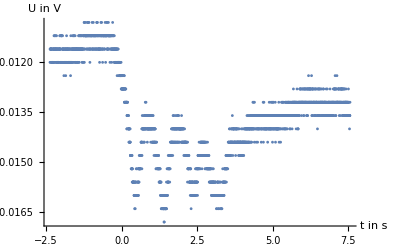

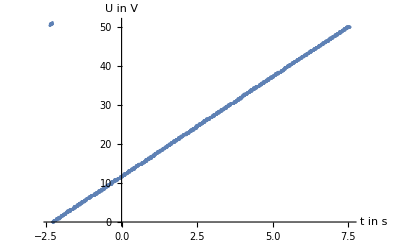

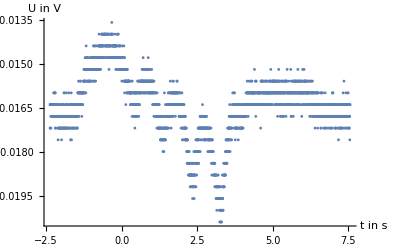

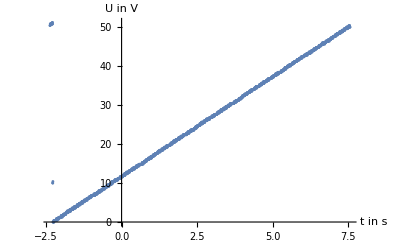

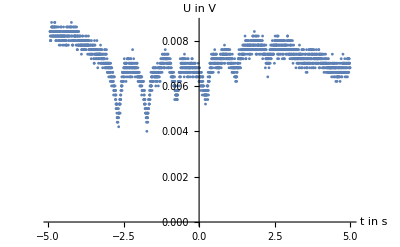

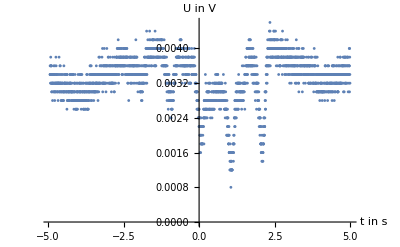

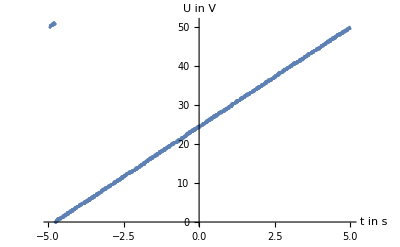

```mathematica
Module[{a,data},
data=Take[rawData,{#1,#1}][[1]]&/@{12,13,14,15,16,17,18};
toFrequency[ch1_,ch2_,min_,max_]:=MapThread[{min+(#2[[2]])/50*(max-min),#1[[2]]}&,{ch1,ch2}];
measurementParameters={
{1,2,9.11,9.32},
{3,4,9.11,9.32},
{5,7,7.95,8.39},
{6,7,7.95,8.39},
};

toFrequency[data[[1]],data[[2]],8.11,8.32];

Print[
ListPlot[
Take[data,{#1,#1}][[1]],
PlotRange->All,PlotStyle->PointSize[0.005],
AxesLabel->{"t in s","U in V"}
]
]&/@Range[7];


Export[NotebookDirectory[]<>"..\\data\\processed\\0011.txt",  Take[rawData,{12,12}][[1]], "Table"];
Export[NotebookDirectory[]<>"..\\data\\processed\\0013.txt",  Take[rawData,{14,14}][[1]], "Table"];
Export[NotebookDirectory[]<>"..\\data\\processed\\0015.txt",  Take[rawData,{16,16}][[1]], "Table"];
Export[NotebookDirectory[]<>"..\\data\\processed\\0016.txt",  Take[rawData,{17,17}][[1]], "Table"];
]
```

```mathematica
,
```